## Offset Curves

```mathematica
OffSetCurve[curve_,dist_]:=Module[{crv = curve, d = dist},
funX=crv[[1]];
funY=crv[[2]];
dx=D[funX,u];
dy=D[funY,u];
offsetX=funX-(d dy)/(√(dx^2+dy^2));
offsetY=funY+(d dx)/(√(dx^2+dy^2));

o={offsetX,offsetY}
]
o=OffSetCurve[{u,u^2/2},0.5]
```

{u-(0.5 u)/(√(1+u^2)),u^2/2+0.5/(√(1+u^2))}

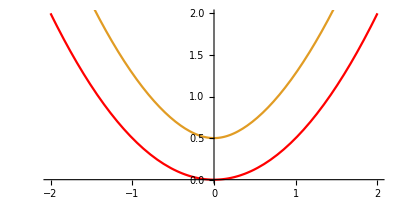

```mathematica
Show[{ParametricPlot[{u,u^2/2},{u,-2,2},PlotStyle->Red],ParametricPlot[o,{u,-2,2}]}]
```